```mathematica
ClearSystemCache[];
ClearAll["Global`*"]
```

```mathematica
Needs["NDSolve`FEM`"] (*for verifying*)
```

### Task & Variables

Solve stationary heat equation in a square 1x1 with Dirichlet boundary conditions (T(Γ)=const=0). Heat source is a Gaussian function with dispersion = 0.2 and maximum of 1. Position of the heat source inside the square is arbitrary. Take P_1(x)P_2(y)  basis functions.

```mathematica
Lx=2;
Ly=2;
σ=0.05;
P0=σ×Sqrt[2π];
```

### Calculation

#### Heat source

```mathematica
Q[x_,y_,x0_,y0_]:=Q[x,y,x0,y0]=P0/(σ×Sqrt[2π])×Exp[(-((x-x0)^2+(y-y0)^2))/σ^2];
```

#### Heat equation & Rayleigh-Ritz Method

Stationary heat equation: -kΔT = -k ((∂^2 T(x,y))/(∂x^2)+(∂^2 T(x,y))/(∂y^2))=Q(x,y)
Final matrix for RR Method: ∑_(n=1)^N <Lφ_m,φ_n>a_n = <Q,φ_m> (<u,v> = ∫_Ω u×v dΩ)
L = ∂^2/(∂x^2)+∂^2/(∂y^2)

```mathematica
L[f_,x_,y_]:=L[f,x,y]=Piecewise[{{0,x==0},{0,y==0}},-Laplacian[f,{x,y}]];
```

Basis functions: φ = x^m y^n(1-x)(1-y) (satisfy Dirichlet boundary conditions)

```mathematica
φ[x_,y_,m_,n_]:=φ[x,y,m,n]=x^m×y^n×(Lx-x)×(Ly-y);
```

Maximum degree of φ

```mathematica
maxDeg = 17;
```

List of basis functions

```mathematica
ClearAll[Φlist]
```

```mathematica
Φtab[x_,y_]:=Φtab[x,y]=Table[φ[x,y,i,j],{i,1,maxDeg-3},{j,1,maxDeg-3}];
Φlist[x_,y_]:=Φlist[x,y]=Module[{myList},myList={};For[i=1,i≤maxDeg-3,i++,For[j=1,j≤maxDeg-3,j++,If[i+j≤maxDeg-2,AppendTo[myList,Φtab[x,y][[i,j]]]]]];myList];
```

```mathematica
n=Length[Φlist[x,y]];
```

Next, we solve the Final matrix equation and get vector of coefficients a_n from it: Ra_n= b

```mathematica
b[x0_,y0_]:=b[x0,y0]=Module[{myb},myb=Table[0,{i,n}];For[i=1,i≤n,i++,myb[[i]]=NIntegrate[Q[x,y,x0,y0]×Φlist[x,y][[i]],{x,0,Lx},{y,0,Ly},Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];myb];
```

```mathematica
R=Table[NIntegrate[L[Φlist[x,y][[i]],x,y]×Φlist[x,y][[j]],{x,0,Lx},{y,0,Ly},Method->{"GlobalAdaptive","SymbolicProcessing"->0}],{i,n},{j,n}];
(*For[i=1,i≤n,i++,
For[j=1,j≤n,j++,R[[i,j]]=NIntegrate[L[Φlist[x,y][[i]],x,y]×Φlist[x,y][[j]],{x,0,Lx},{y,0,Ly}]]];*)
```

```mathematica
a[x0_,y0_]:=a[x0,y0]=LinearSolve[R,b[x0,y0]];
```

Finally, we get the approximating function T(x,y) = ∑_(n=1)^N  a_n×φ_n(x,y)

```mathematica
Trr[x_,y_,x0_,y0_]:=Trr[x,y,x0,y0]=Sum[a[x0,y0][[i]]×Φlist[x,y][[i]],{i,n}];
```

### Solution: Temperature distribution in the region

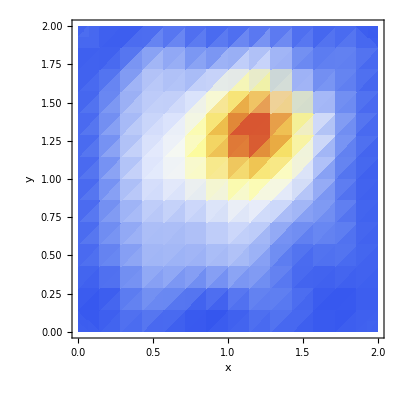

```mathematica
DensityPlot[Trr[x,y,1.2,1.3],{x,0,Lx},{y,0,Ly},FrameLabel->{x,y},ColorFunction->"TemperatureMap",PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"Temperature, K"]]
```

### Verification

```mathematica
ClearAll[sol,Tfem]
```

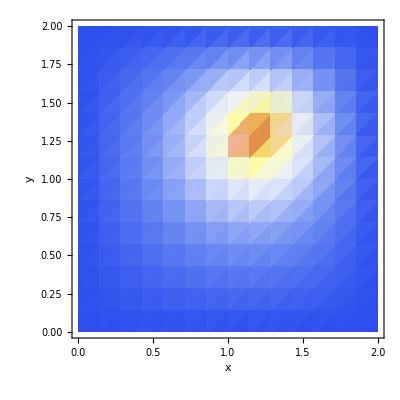

```mathematica
sol=NDSolve[{-D[D[T[x,y],x],x]-D[D[T[x,y],y],y]==Q[x,y,1.2,1.3],T[0,y]==0,T[Lx,y]==0,T[x,Ly]==0,T[x,0]==0},T[x,y],{x,0,Lx},{y,0,Ly}];
Tfem[x_,y_]:=Tfem[x,y]=T[x,y]/.sol
DensityPlot[Tfem[x,y],{x,0,Lx},{y,0,Ly},ColorFunction->"TemperatureMap",FrameLabel->{x,y},PlotRange->All,PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"Temperature, K"]]
```